1/10

{}

{1.5}

{1.5,1.25}

{1.5,1.25,1.375}

{1.5,1.25,1.375,1.4375}

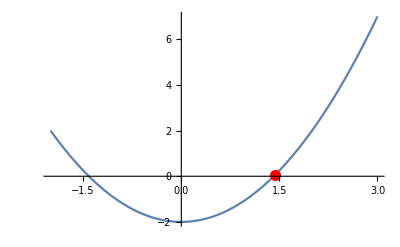

```mathematica
(*raveshe do bakhsi*)
ClearAll;
a=1;
b=2;
f[x_]:=x^2-2;
i=0;
e=10^-1

list={}

While[Abs[a-b]>e,i++;
c=(a+b)/2;
AppendTo[list,N[c]];
Print[list];

If[f[a]*f[c]<0,b=c,a=c];
]
Plot[f[x],{x,-2,3}, Epilog->{Red,PointSize[0.02],Point[{c,f[c]}]},GridLines->{{c},None} ,GridLinesStyle->Directive[Dotted, Gray]]
```